```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lindgreo/Desktop

```mathematica
test=<<"MinesStates.txt"
```

Syntax::sntx: 
   Invalid syntax in or before "*************"
                                  ^
     (line 1 of "MinesStates.txt").

```mathematica
str = OpenRead["MinesStates.txt"];
```

```mathematica
Close[str]
```

MinesStates.txt

```mathematica
line = Read[str,String]
```

1,1

```mathematica
StringMatchQ[line,"*Mines start*"]
StringMatchQ["Mines start*",Number_~~]
```

True

False

```mathematica
firstChar = Characters[line][[1]]
```

1

```mathematica
firstChar
```

```mathematica
line
```

*Mines start*

```mathematica
StringMatchQ[firstChar,DigitCharacter]
```

True

```mathematica
RandomReal[0.1{-1,1},{2}]
```

{0.0234319,-0.0322185}

```mathematica
line
```

```mathematica
randomCirc[r_]:=Module[{rr},
rr = RandomReal[r{-1,1},{2}];
While[Norm[rr]>r,
rr = RandomReal[r{-1,1},{2}];
];
rr
]
```

```mathematica
str = OpenRead["MinesStates.txt"];
line = Read[str,String];
t = 0;
coordList = {};
tempCoordList = {};
While[line[[0]]==String&&t<1000000,
line = Read[str,String];
firstChar = Characters[line][[1]];
If[StringMatchQ[firstChar,DigitCharacter],
AppendTo[tempCoordList,randomCirc[0.1]+{{0,1},{-1,0}}.ToExpression["{"<>line<>"}"]];
];
If[StringMatchQ[line,"*Mines start*"],
AppendTo[coordList,tempCoordList];
tempCoordList = {};
t++;
];
];
AppendTo[coordList,tempCoordList];
Close[str];
coordList= 
coordList[[2;;]];
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[EndOfFile, DigitCharacter].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[EndOfFile, "*Mines start*"].

```mathematica
minesCoords = {{5,-2},{7,-1},{8,-1},{9,-3},{10,-3},{11,-3}};
goalC = {{10,-4}};
```

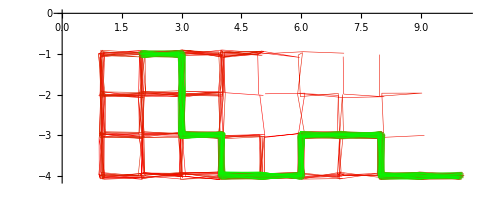

```mathematica
path = ListLinePlot[coordList[[;;100]],AspectRatio-> Automatic,PlotStyle-> Table[{Thickness[0.001],RGBColor[1-i/100,i/100,0]},{i,100}]]
```



```mathematica
m1 = Graphics[{Black,Disk[]}]
```

```mathematica
m2 =  Graphics[{RGBColor[0.9,0.9,0],Disk[]}];
```

```mathematica
mines = ListPlot[minesCoords,PlotMarkers-> {m1,0.1}];
goal = ListPlot[goalC,PlotMarkers-> {m2,0.18}];
```

```mathematica
border = ListLinePlot[{{0.5,-0.5},{16.5,-0.5},{16.5,-4.5},{0.5,-4.5},{0.5,-0.5}},PlotStyle-> Thick];
```

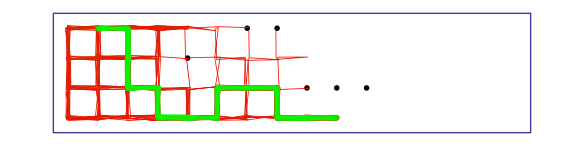

```mathematica
Show[mines,border,goal,path,PlotRange-> {{0,15},{0,-5}},AspectRatio-> Automatic,Axes-> False]
```

```mathematica
minesImages = Table[
path = ListLinePlot[coordList[[;;ii]],AspectRatio-> Automatic,PlotStyle-> Table[{Thickness[0.001],RGBColor[1-i/100,i/100,0]},{i,ii}]];
Show[mines,border,goal,path,PlotRange-> {{0,15},{0,-5}},AspectRatio-> Automatic,Axes-> False]
,{ii,100}];
```

```mathematica
ListAnimate[minesImages]
```

```mathematica
minesFig = -Graphics-;
```

```mathematica
Directory[]
```

/Users/lindgreo/Desktop

## PLOT

```mathematica
massaData = {{{0,0},1902},{{0,1},-45},{{0,2},-45},{{0,3},-45},{{0,4},-45},{{0,5},-45},{{0,6},-45},{{0,7},-45},{{0,8},-45},{{0,9},-45},{{0,10},-45},{{0,11},-45},{{0,12},-45},{{0,13},-45},{{0,14},-45},{{0,15},-45},{{0,16},-45},{{0,17},-45},{{1,0},-45},{{1,1},-45},{{1,2},-45},{{1,3},-45},{{1,4},-45},{{1,5},-45},{{1,6},-45},{{1,7},-45},{{1,8},-45},{{1,9},-45},{{1,10},-45},{{1,11},-45},{{1,12},-45},{{1,13},-45},{{1,14},-45},{{1,15},-45},{{1,16},-45},{{1,17},-45},{{2,0},-45},{{2,1},-45},{{2,2},-45},{{2,3},-45},{{2,4},-45},{{2,5},-45},{{2,6},-45},{{2,7},-45},{{2,8},-45},{{2,9},-45},{{2,10},-45},{{2,11},-45},{{2,12},-45},{{2,13},-45},{{2,14},-45},{{2,15},-45},{{2,16},-45},{{2,17},-45},{{3,0},-45},{{3,1},-45},{{3,2},-45},{{3,3},-45},{{3,4},-45},{{3,5},-45},{{3,6},-45},{{3,7},-45},{{3,8},-45},{{3,9},-45},{{3,10},-45},{{3,11},-45},{{3,12},-45},{{3,13},-45},{{3,14},-45},{{3,15},-45},{{3,16},-45},{{3,17},-45},{{4,0},-45},{{4,1},-45},{{4,2},-45},{{4,3},-45},{{4,4},-45},{{4,5},-45},{{4,6},-45},{{4,7},-45},{{4,8},-45},{{4,9},-45},{{4,10},-45},{{4,11},1955},{{4,12},1946},{{4,13},1937},{{4,14},1928},{{4,15},1919},{{4,16},1910},{{4,17},-45},{{5,0},-45},{{5,1},-45},{{5,2},-45},{{5,3},-45},{{5,4},-45},{{5,5},-45},{{5,6},-45},{{5,7},-45},{{5,8},-45},{{5,9},-45},{{5,10},-45},{{5,11},-45},{{5,12},-45},{{5,13},-45},{{5,14},-45},{{5,15},-45},{{5,16},-45},{{5,17},-45}};
```

```mathematica
Tally[massaData[[All,2]]]
```

{{1902,1},{-45,101},{1955,1},{1946,1},{1937,1},{1928,1},{1919,1},{1910,1}}

```mathematica
maxX= Max[massaData[[All,1,1]]];
maxY= Max[massaData[[All,1,2]]];
```

```mathematica
graph = Table[0,{maxX+1},{maxY+1}];
Do[graph[[d[[1,1]]+1,d[[1,2]]+1]] = d[[2]],{d,massaData}];
```

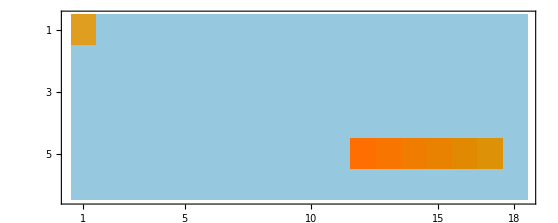

```mathematica
MatrixPlot[graph]
```